```mathematica
Sum[1/(n(π n)^(1/2)),{n,1,∞}]
```

Zeta[3/2]/(√π)

```mathematica
4/(n(π n)^(1/2))-1/(n+1)((2n)!)/(n!)^2
```

4/(n^(3/2) √π)-((2 n)!)/((1+n) (n!)^2)

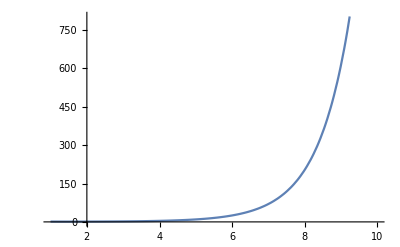

```mathematica
Plot[{4^n/(n(π n)^(1/2))-CatalanNumber[n]},{n,1,10}]
```

```mathematica
4^n/(n^(3/2)(π)^(1/2))-4^n/((n+1)(π n)^(1/2))//FullSimplify
```

```mathematica
Simplify[{4^n/(n^(3/2) (1+n) √π)==4(√2)/(√π)-2},n]
```

{2+4^True/(√π True^(3/2) (1+True))==4 √(2/π)}

```mathematica
Solve[D[4^n/(n^(3/2) (1+n) √π),n]==0,n]
```

{{n→(5-2 Log[4]-√(25+4 Log[4]+4 Log[4]^2))/(4 Log[4])},{n→(5-2 Log[4]+√(25+4 Log[4]+4 Log[4]^2))/(4 Log[4])}}

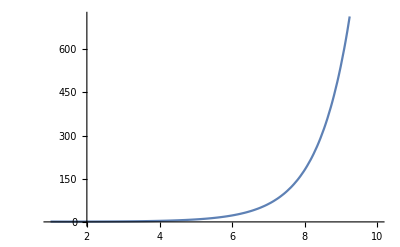

```mathematica
Plot[4^n/(n^(3/2) (1+n) √π),{n,1,10}]
```

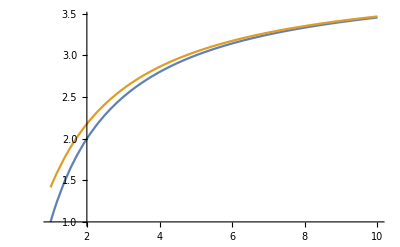

```mathematica
Plot[{(4n-2)/(n+1),(4 n^(3/2))/(1+n)^(3/2)},{n,1,10},PlotRange->Full]
```

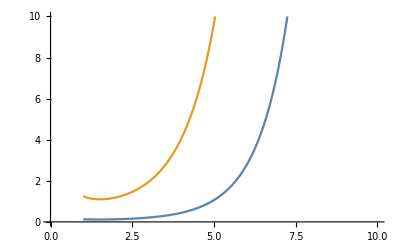

```mathematica
Plot[{4^n/((n+1)(π n)^(1/2))-CatalanNumber[n],4^n/(n(π n)^(1/2))-CatalanNumber[n]},{n,1,10},PlotRange->{0,10}]
```

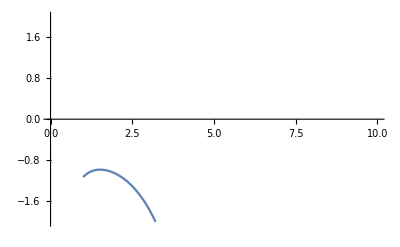

```mathematica
Plot[{4^n/((n+1)(π n)^(1/2))-4^n/(n(π n)^(1/2))},{n,1,10},PlotRange->{-2,2}]
```

```mathematica
4^n/((n+1)(π n)^(1/2))-4^n/(n(π n)^(1/2))/.n->2
```

-(4 √(2/π))/3

```mathematica
Solve[D[4^n/((n+1)(π n)^(1/2))-4^n/(n(π n)^(1/2)),n]==0,n]
```

{{n→(5-2 Log[4]-√(25+4 Log[4]+4 Log[4]^2))/(4 Log[4])},{n→(5-2 Log[4]+√(25+4 Log[4]+4 Log[4]^2))/(4 Log[4])}}